```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/368nm.dat"]
data1hour=Drop[data1, None,1]
data2 = Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/412nm.dat"]
data2hour=Drop[data2,None,1]
data3 = Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/500nm.dat"]
data3hour=Drop[data3,None,1]
data4 = Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/610nm.dat"]
data4hour=Drop[data4,None,1]
data5 = Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/675nm.dat"]
data5hour=Drop[data5,None,1]
data6= Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/778nm.dat"]
data6hour=Drop[data6,None,1]
data7 = Import["/net/home/f09/bajennissen/research/DAY207/tau_day_data/862nm.dat"]
data7hour=Drop[data7,None,1]
```

{{207.344,8.25,0.247067},{207.351,8.41667,0.253794},{207.36,8.65,0.242768},{207.368,8.83333,0.213584},{207.375,9,0.226846},{207.383,9.18333,0.211423},{207.389,9.33333,0.192229},{207.396,9.5,0.204995},{207.405,9.71667,0.220294},{207.413,9.9,0.239056},{207.422,10.1333,0.201638},{207.428,10.2833,0.242688},{207.435,10.45,0.354102},{207.442,10.6167,0.397009},{207.449,10.7833,0.467967},{207.456,10.95,0.524938},{207.465,11.15,0.62189},{207.472,11.3167,1.08539},{207.478,11.4833,1.0069},{207.484,11.6167,0.832249},{207.489,11.7333,0.780801},{207.492,11.8167,0.774335},{207.504,12.1,0.412656},{207.512,12.3,0.320036},{207.519,12.4667,0.191984},{207.526,12.6167,0.124838},{207.548,13.15,0.160512},{207.563,13.5167,0.180969},{207.574,13.7667,0.126718},{207.585,14.0333,0.101907},{207.597,14.3333,0.111198},{207.615,14.75,0.118253},{207.626,15.0167,0.120537}}

{{8.25,0.247067},{8.41667,0.253794},{8.65,0.242768},{8.83333,0.213584},{9,0.226846},{9.18333,0.211423},{9.33333,0.192229},{9.5,0.204995},{9.71667,0.220294},{9.9,0.239056},{10.1333,0.201638},{10.2833,0.242688},{10.45,0.354102},{10.6167,0.397009},{10.7833,0.467967},{10.95,0.524938},{11.15,0.62189},{11.3167,1.08539},{11.4833,1.0069},{11.6167,0.832249},{11.7333,0.780801},{11.8167,0.774335},{12.1,0.412656},{12.3,0.320036},{12.4667,0.191984},{12.6167,0.124838},{13.15,0.160512},{13.5167,0.180969},{13.7667,0.126718},{14.0333,0.101907},{14.3333,0.111198},{14.75,0.118253},{15.0167,0.120537}}

{{207.344,8.25,0.237308},{207.351,8.41667,0.246208},{207.36,8.65,0.245056},{207.368,8.83333,0.220153},{207.375,9,0.22211},{207.383,9.18333,0.211256},{207.389,9.33333,0.207044},{207.396,9.5,0.213249},{207.405,9.71667,0.226714},{207.413,9.9,0.252836},{207.422,10.1333,0.234913},{207.428,10.2833,0.250178},{207.435,10.45,0.306058},{207.442,10.6167,0.327742},{207.449,10.7833,0.36141},{207.456,10.95,0.399931},{207.465,11.15,0.435354},{207.472,11.3167,0.590884},{207.478,11.4833,0.575572},{207.484,11.6167,0.517734},{207.489,11.7333,0.490295},{207.492,11.8167,0.501073},{207.504,12.1,0.324805},{207.512,12.3,0.287084},{207.519,12.4667,0.209415},{207.526,12.6167,0.174241},{207.548,13.15,0.214715},{207.563,13.5167,0.227944},{207.574,13.7667,0.169341},{207.585,14.0333,0.145483},{207.597,14.3333,0.156496},{207.615,14.75,0.155227},{207.626,15.0167,0.166538}}

{{8.25,0.237308},{8.41667,0.246208},{8.65,0.245056},{8.83333,0.220153},{9,0.22211},{9.18333,0.211256},{9.33333,0.207044},{9.5,0.213249},{9.71667,0.226714},{9.9,0.252836},{10.1333,0.234913},{10.2833,0.250178},{10.45,0.306058},{10.6167,0.327742},{10.7833,0.36141},{10.95,0.399931},{11.15,0.435354},{11.3167,0.590884},{11.4833,0.575572},{11.6167,0.517734},{11.7333,0.490295},{11.8167,0.501073},{12.1,0.324805},{12.3,0.287084},{12.4667,0.209415},{12.6167,0.174241},{13.15,0.214715},{13.5167,0.227944},{13.7667,0.169341},{14.0333,0.145483},{14.3333,0.156496},{14.75,0.155227},{15.0167,0.166538}}

{{207.344,8.25,0.189247},{207.351,8.41667,0.192614},{207.36,8.65,0.195888},{207.368,8.83333,0.17262},{207.375,9,0.176459},{207.383,9.18333,0.172732},{207.389,9.33333,0.164999},{207.396,9.5,0.170776},{207.405,9.71667,0.180589},{207.413,9.9,0.204352},{207.422,10.1333,0.179394},{207.428,10.2833,0.192463},{207.435,10.45,0.208814},{207.442,10.6167,0.204875},{207.449,10.7833,0.225333},{207.456,10.95,0.236576},{207.465,11.15,0.246146},{207.472,11.3167,0.279048},{207.478,11.4833,0.261891},{207.484,11.6167,0.257193},{207.489,11.7333,0.252498},{207.492,11.8167,0.26331},{207.504,12.1,0.181914},{207.512,12.3,0.188797},{207.519,12.4667,0.154444},{207.526,12.6167,0.144305},{207.548,13.15,0.184493},{207.563,13.5167,0.204349},{207.574,13.7667,0.137974},{207.585,14.0333,0.124733},{207.597,14.3333,0.130751},{207.615,14.75,0.138123},{207.626,15.0167,0.133436}}

{{8.25,0.189247},{8.41667,0.192614},{8.65,0.195888},{8.83333,0.17262},{9,0.176459},{9.18333,0.172732},{9.33333,0.164999},{9.5,0.170776},{9.71667,0.180589},{9.9,0.204352},{10.1333,0.179394},{10.2833,0.192463},{10.45,0.208814},{10.6167,0.204875},{10.7833,0.225333},{10.95,0.236576},{11.15,0.246146},{11.3167,0.279048},{11.4833,0.261891},{11.6167,0.257193},{11.7333,0.252498},{11.8167,0.26331},{12.1,0.181914},{12.3,0.188797},{12.4667,0.154444},{12.6167,0.144305},{13.15,0.184493},{13.5167,0.204349},{13.7667,0.137974},{14.0333,0.124733},{14.3333,0.130751},{14.75,0.138123},{15.0167,0.133436}}

{{207.344,8.25,0.179397},{207.351,8.41667,0.182246},{207.36,8.65,0.183762},{207.368,8.83333,0.166038},{207.375,9,0.173958},{207.383,9.18333,0.165568},{207.389,9.33333,0.160904},{207.396,9.5,0.166258},{207.405,9.71667,0.174072},{207.413,9.9,0.187459},{207.422,10.1333,0.165227},{207.428,10.2833,0.176792},{207.435,10.45,0.192904},{207.442,10.6167,0.19912},{207.449,10.7833,0.221671},{207.456,10.95,0.23426},{207.465,11.15,0.24798},{207.472,11.3167,0.302026},{207.478,11.4833,0.254606},{207.484,11.6167,0.270486},{207.489,11.7333,0.266164},{207.492,11.8167,0.264976},{207.504,12.1,0.178596},{207.512,12.3,0.182467},{207.519,12.4667,0.146668},{207.526,12.6167,0.144964},{207.548,13.15,0.175835},{207.563,13.5167,0.196776},{207.574,13.7667,0.123378},{207.585,14.0333,0.122907},{207.597,14.3333,0.125086},{207.615,14.75,0.130528},{207.626,15.0167,0.119487}}

{{8.25,0.179397},{8.41667,0.182246},{8.65,0.183762},{8.83333,0.166038},{9,0.173958},{9.18333,0.165568},{9.33333,0.160904},{9.5,0.166258},{9.71667,0.174072},{9.9,0.187459},{10.1333,0.165227},{10.2833,0.176792},{10.45,0.192904},{10.6167,0.19912},{10.7833,0.221671},{10.95,0.23426},{11.15,0.24798},{11.3167,0.302026},{11.4833,0.254606},{11.6167,0.270486},{11.7333,0.266164},{11.8167,0.264976},{12.1,0.178596},{12.3,0.182467},{12.4667,0.146668},{12.6167,0.144964},{13.15,0.175835},{13.5167,0.196776},{13.7667,0.123378},{14.0333,0.122907},{14.3333,0.125086},{14.75,0.130528},{15.0167,0.119487}}

{{207.344,8.25,0.141223},{207.351,8.41667,0.146553},{207.36,8.65,0.151422},{207.368,8.83333,0.136334},{207.375,9,0.136981},{207.383,9.18333,0.139054},{207.389,9.33333,0.133701},{207.396,9.5,0.138582},{207.405,9.71667,0.148706},{207.413,9.9,0.160408},{207.422,10.1333,0.139996},{207.428,10.2833,0.15212},{207.435,10.45,0.188256},{207.442,10.6167,0.198051},{207.449,10.7833,0.231808},{207.456,10.95,0.24339},{207.465,11.15,0.27501},{207.472,11.3167,0.380022},{207.478,11.4833,0.323487},{207.484,11.6167,0.340467},{207.489,11.7333,0.319509},{207.492,11.8167,0.315863},{207.504,12.1,0.192924},{207.512,12.3,0.179993},{207.519,12.4667,0.138969},{207.526,12.6167,0.125713},{207.548,13.15,0.150866},{207.563,13.5167,0.177039},{207.574,13.7667,0.0981186},{207.585,14.0333,0.103247},{207.597,14.3333,0.0977907},{207.615,14.75,0.101089},{207.626,15.0167,0.091588}}

{{8.25,0.141223},{8.41667,0.146553},{8.65,0.151422},{8.83333,0.136334},{9,0.136981},{9.18333,0.139054},{9.33333,0.133701},{9.5,0.138582},{9.71667,0.148706},{9.9,0.160408},{10.1333,0.139996},{10.2833,0.15212},{10.45,0.188256},{10.6167,0.198051},{10.7833,0.231808},{10.95,0.24339},{11.15,0.27501},{11.3167,0.380022},{11.4833,0.323487},{11.6167,0.340467},{11.7333,0.319509},{11.8167,0.315863},{12.1,0.192924},{12.3,0.179993},{12.4667,0.138969},{12.6167,0.125713},{13.15,0.150866},{13.5167,0.177039},{13.7667,0.0981186},{14.0333,0.103247},{14.3333,0.0977907},{14.75,0.101089},{15.0167,0.091588}}

{{207.344,8.25,0.139953},{207.351,8.41667,0.143707},{207.36,8.65,0.155555},{207.368,8.83333,0.139642},{207.375,9,0.142128},{207.383,9.18333,0.149798},{207.389,9.33333,0.146263},{207.396,9.5,0.160849},{207.405,9.71667,0.170836},{207.413,9.9,0.17973},{207.422,10.1333,0.172287},{207.428,10.2833,0.187674},{207.435,10.45,0.26782},{207.442,10.6167,0.349709},{207.449,10.7833,0.387207},{207.456,10.95,0.444712},{207.465,11.15,0.520868},{207.472,11.3167,0.933486},{207.478,11.4833,0.76475},{207.484,11.6167,0.732344},{207.489,11.7333,0.696799},{207.492,11.8167,0.630648},{207.504,12.1,0.359564},{207.512,12.3,0.277536},{207.519,12.4667,0.20248},{207.526,12.6167,0.168826},{207.548,13.15,0.160858},{207.563,13.5167,0.191317},{207.574,13.7667,0.116203},{207.585,14.0333,0.1243},{207.597,14.3333,0.112124},{207.615,14.75,0.110579},{207.626,15.0167,0.101595}}

{{8.25,0.139953},{8.41667,0.143707},{8.65,0.155555},{8.83333,0.139642},{9,0.142128},{9.18333,0.149798},{9.33333,0.146263},{9.5,0.160849},{9.71667,0.170836},{9.9,0.17973},{10.1333,0.172287},{10.2833,0.187674},{10.45,0.26782},{10.6167,0.349709},{10.7833,0.387207},{10.95,0.444712},{11.15,0.520868},{11.3167,0.933486},{11.4833,0.76475},{11.6167,0.732344},{11.7333,0.696799},{11.8167,0.630648},{12.1,0.359564},{12.3,0.277536},{12.4667,0.20248},{12.6167,0.168826},{13.15,0.160858},{13.5167,0.191317},{13.7667,0.116203},{14.0333,0.1243},{14.3333,0.112124},{14.75,0.110579},{15.0167,0.101595}}

{{207.344,8.25,0.112564},{207.351,8.41667,0.126766},{207.36,8.65,0.114881},{207.368,8.83333,0.125353},{207.375,9,0.109345},{207.383,9.18333,0.14374},{207.389,9.33333,0.117309},{207.396,9.5,0.131575},{207.405,9.71667,0.134083},{207.413,9.9,0.150441},{207.422,10.1333,0.123633},{207.428,10.2833,0.168182},{207.435,10.45,0.332863},{207.442,10.6167,0.507759},{207.449,10.7833,0.642507},{207.456,10.95,0.775544},{207.465,11.15,0.982315},{207.472,11.3167,6.24627},{207.478,11.4833,3.05876},{207.484,11.6167,2.2488},{207.489,11.7333,1.73257},{207.492,11.8167,1.47984},{207.504,12.1,0.618849},{207.512,12.3,0.385405},{207.519,12.4667,0.22495},{207.526,12.6167,0.157181},{207.548,13.15,0.135893},{207.563,13.5167,0.158696},{207.574,13.7667,0.0851916},{207.585,14.0333,0.0873779},{207.597,14.3333,0.087476},{207.615,14.75,0.0854141},{207.626,15.0167,0.0737482}}

{{8.25,0.112564},{8.41667,0.126766},{8.65,0.114881},{8.83333,0.125353},{9,0.109345},{9.18333,0.14374},{9.33333,0.117309},{9.5,0.131575},{9.71667,0.134083},{9.9,0.150441},{10.1333,0.123633},{10.2833,0.168182},{10.45,0.332863},{10.6167,0.507759},{10.7833,0.642507},{10.95,0.775544},{11.15,0.982315},{11.3167,6.24627},{11.4833,3.05876},{11.6167,2.2488},{11.7333,1.73257},{11.8167,1.47984},{12.1,0.618849},{12.3,0.385405},{12.4667,0.22495},{12.6167,0.157181},{13.15,0.135893},{13.5167,0.158696},{13.7667,0.0851916},{14.0333,0.0873779},{14.3333,0.087476},{14.75,0.0854141},{15.0167,0.0737482}}

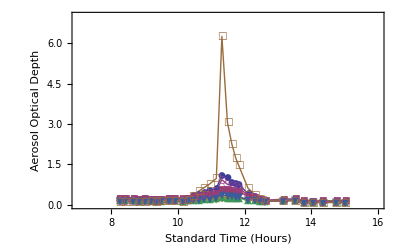

```mathematica
<<PlotLegends`
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotLegend->{"368nm","412nm","500nm","610nm","675nm","778nm","862nm"},LegendPosition->{1.1,-0.4}, LegendSize->{0.5,0.75},PlotRange->{{7,16},{0,7}},Frame->True, AxesOrigin-> {7,0},LegendShadow->None,FrameLabel->{{"Aerosol Optical Depth",""},{"Standard Time (Hours)","Day 207 July 26th, 2010"}}]
```

```mathematica
(* clouds are to blame for the big spike in the 862nm
```